# Lesson 4 log · Building our own: a transformer that expands tensor-algebra expressions

Written 2026-11-24 02:06 UTC by lesson4_build_your_own.nb. 9 of 9 checks pass.

This lesson assembles Lessons 1–3 on our own problem. Lesson 1: encoder–decoder and beam search. Lesson 2: uniform tree sampling, prefix notation and verification by an exact oracle. Lesson 3: the transformer parts, shared embeddings, label smoothing and the warm-up schedule.

## 1. The task and the data

Expand: the source is an expression written as one would type it, the target is its full expansion in prefix notation. Trees are drawn uniformly with Algorithm 1 of Lample and Charton (Lesson 2), with 1 to 5 operators, each ⨂ or ⨁, over the atoms a, b, c, d. ⨂ binds tighter than ⨁, so only a ⨁ inside a ⨂ needs parentheses.

source (infix) | target (expansion, prefix)
  a⨁b |   ⨁ab
  c⨂b⨂(a⨁c)⨂b |   ⨁⨂c⨂b⨂ab⨂c⨂b⨂cb
  c⨂c⨂c⨁d |   ⨁⨂c⨂ccd
  d⨁d⨁d⨂(a⨁a⨂a) |   ⨁d⨁d⨁⨂da⨂d⨂aa

PASS  the tree sampler reaches all 14 binary trees with 4 operators, about equally often (counts 950…1060 out of 14,000)

## 2. The oracle

An expression is a list of words, each word an ordered ⨂-product of atoms. ⨁ joins two lists; ⨂ multiplies every word of the left by every word of the right, keeping their order (⨂ is not commutative). Two expressions are equal when their lists of words agree up to order (⨁ is commutative up to isomorphism). This is the check tnEquivalentQ makes in TensorNets.

words(x) = {x}     words(A ⨁ B) = words(A) ∪ words(B)     words(A ⨂ B) = { u v : u ∈ words(A), v ∈ words(B) }

PASS  (a⨁b)⨂c expands to a⨂c ⨁ b⨂c, i.e. ⨁ ⨂ a c ⨂ b c

PASS  the oracle accepts a⨂c ⨁ b⨂c in either order, and rejects c⨂a ⨁ c⨂b (the order of factors matters)

PASS  for 500 random pairs the target is a valid prefix tree equivalent to the source

## 3. The net, assembled from the parts of Lesson 3

The encoder–decoder of Lesson 3: shared embeddings multiplied by √d, sinusoidal positions, 2 encoder and 2 decoder layers with 4 heads, d = 32, dff = 128. Source and target share one vocabulary of 10 tokens, so one array serves both embeddings and the output projection. The decoder reads the target without its last token (teacher forcing) and is trained to predict it without its first, against label-smoothed targets (ϵ = 0.1), with Adam (β₂ = 0.98) and the warm-up schedule (400 steps).

-Graphics-

PASS  the model has 59950 parameters, and one shared array of 320 for the three embeddings

12000 training pairs and 100 test pairs; no test source appears in the training set.

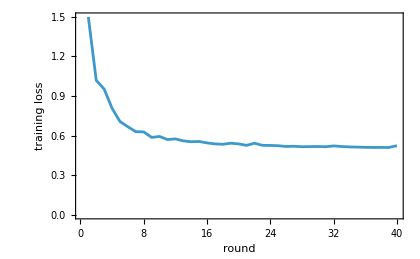

Training took 211 s for 40 rounds. The loss cannot reach 0: with label smoothing its floor is the entropy of the smoothed target.

PASS  the training loss fell by more than half (from 1.5 to 0.524)

PASS  after training, the three embeddings are still one shared array

## 4. Decoding and checking

Each test source is decoded three ways: greedy (a beam of width 1) with no constraint; a beam of width 4 with the length penalty α = 0.6 and no constraint; and the same beam constrained by the prefix grammar, which allows </s> only when the tree is complete and nothing else then. Every answer is checked by the oracle. As in Lample and Charton, 'any in beam' counts a source as solved if any hypothesis in the beam passes the check.

decoding (100 test sources) | valid prefix | same tokens as the oracle | top answer verified | any in beam verified
greedy | 99% | 93% | 93% | 93%
beam 4 | 100% | 94% | 94% | 99%
beam 4 + grammar | 100% | 94% | 94% | 99%

source | top answer (beam + grammar) | verified
  d⨂(c⨁b⨂c⨁c)⨂d |   ⨁⨂d⨂cd⨁⨂d⨂b⨂cd⨂d⨂cd | True
  c⨁d⨁a⨂a⨁c |   ⨁c⨁d⨁⨂aac | True
  d⨂c⨁c⨁b⨁c⨂d |   ⨁⨂dc⨁c⨁b⨂cd | True
  a⨂(c⨁a⨁d)⨁c⨁b |   ⨁⨂ac⨁⨂aa⨁⨂ad⨁cb | True
  a⨂a⨁d⨁a⨁d |   ⨁⨂aa⨁d⨁ad | True
  b⨂b⨁b |   ⨁⨂bbb | True
  d⨂a |   ⨂da | True
  a⨂(d⨁a⨂b) |   ⨁⨂ad⨂a⨂ab | True

PASS  with the grammar as a constraint every answer is a valid prefix tree

PASS  'any in beam' is never below 'top answer' (it counts the top answer too)

What to try next: more training pairs or rounds (owSettings), a larger d, or a curriculum from short to long expressions. A single wrong token spoils a whole expansion, so longer targets are harder; the oracle shows exactly which answers are wrong.

## Where this goes in TensorNets

tnParserNet in ff_tensornets_new.nb is this same kind of encoder–decoder, mapping tokens to the prefix tree; tnPolicyNet and tnValueNet reuse the encoder. The difference in the release is that simplification is done by the policy net choosing rewrite rules, which the exact engine applies, so every step is sound, rather than by writing the whole answer at once as here.

© Computational Classnotes · CC BY-NC-SA 4.0